```mathematica
用参数方程法计算三相载流导线截面上不同时刻的磁力线
```

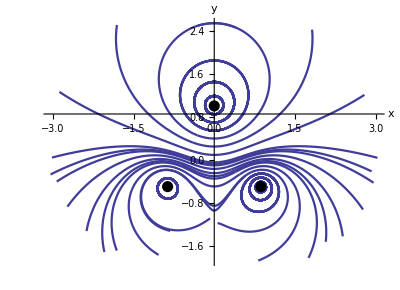

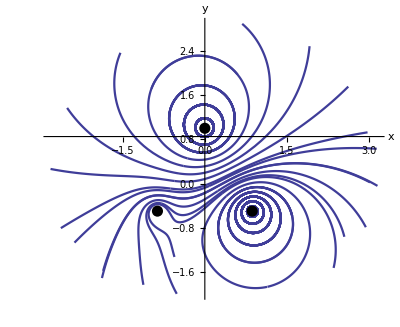

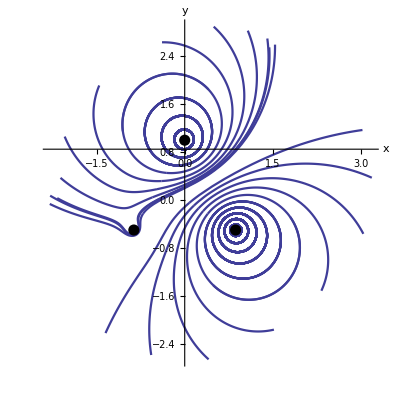

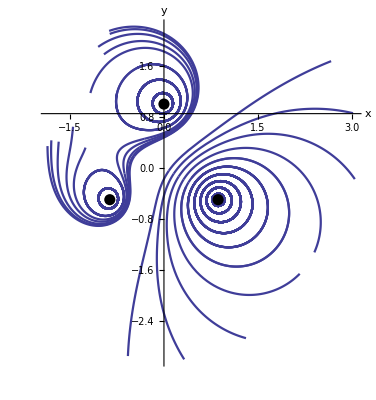

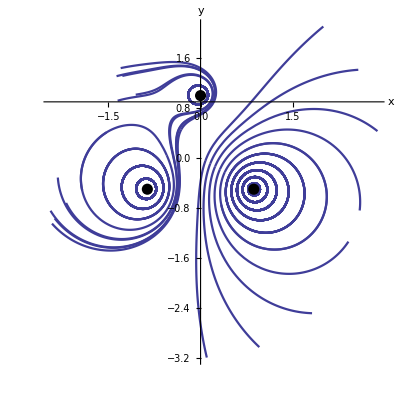

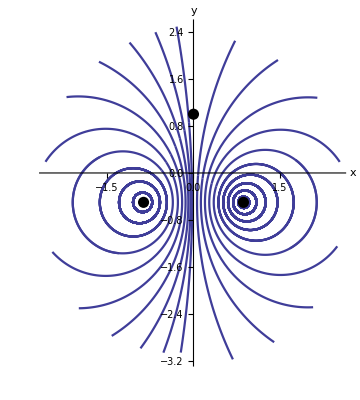

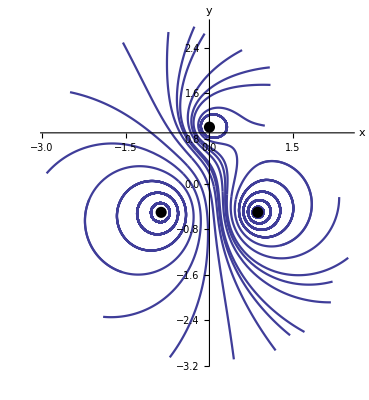

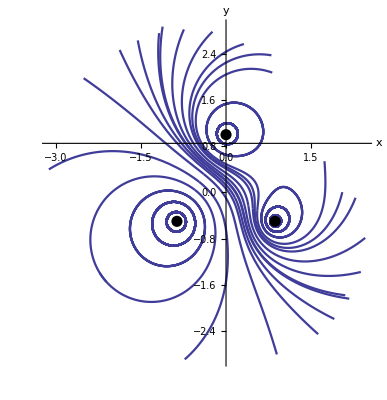

-Graphics-

```mathematica
d=1.0;ω=2π*50.0;ξm=2.0π;
p1={0,d};p2=d {-Cos[π/6],-Sin[π/6]};
p3=d {Cos[π/6],-Sin[π/6]};p={};
(*............starting points..........*)
Do[
AppendTo[p,p1+(p2-p1)*j/11];
AppendTo[p,p3*j/11],
{j,10}]
(*............defining functions.......*)
Bx[x_,y_]:=
(i1*(y-d))/((x-0)^2+(y-d)^2)+(i2*(y+d/2))/((x+d*√3/2)^2+(y+d/2)^2)+
(i3*(y+d/2))/((x-d*√3/2)^2+(y+d/2)^2);
By[x_,y_]:=
-((i1*x)/((x-0)^2+(y-d)^2)+(i2*(x+d*√3/2))/((x+d*√3/2)^2+(y+d/2)^2)+
(i3*(x-d*√3/2))/((x-d*√3/2)^2+(y+d/2)^2));
(*...computating magnetic line of force...*)
Do[
{i1,i2,i3}={Cos[ω t0],Cos[ω t0-2π/3],
Cos[ω t0-4π/3]};
(*......forward direction............*)
forceline={};
equ1={x'[ξ]==Bx[x[ξ],y[ξ]],y'[ξ]==By[x[ξ],y[ξ]],
x[0]==x0,y[0]==y0};
Do[
x0=p[[j,1]];y0=p[[j,2]];
s=NDSolve[equ1,{x,y},{ξ,0,ξm}];
{x,y}={x,y}/.s[[1]];
g=ParametricPlot[{x[ξ],y[ξ]},{ξ,0,ξm},
PlotStyle->Thickness[0.004]];
AppendTo[forceline,g];Clear[x,y,x0,y0],
{j,20}];
g1=Show[forceline];
(*......opposite direction............*)
forceline={};
equ2={x'[ξ]==-Bx[x[ξ],y[ξ]],
y'[ξ]==-By[x[ξ],y[ξ]],x[0]==x0,y[0]==y0};
Do[
x0=p[[j,1]];y0=p[[j,2]];
s=NDSolve[equ2,{x,y},{ξ,0,ξm}];
{x,y}={x,y}/.s[[1]];
g=ParametricPlot[{x[ξ],y[ξ]},{ξ,0,ξm},
PlotStyle->Thickness[0.004]];
AppendTo[forceline,g];Clear[x,y,x0,y0],
{j,20}];
g2=Show[forceline];
(*...........composition...........*)
g=Show[{g1,g2},AxesStyle->Thickness[0.003],
PlotRange->All,AxesLabel->{"x","y"},
Epilog->{PointSize[0.02],Point/@{p1,p2,p3}}];
Print[g],
{t0,0,2π/ω,2π/ω/20}]
Clear[Bx,By,i1,i2,i3,x0,y0]
```